# Met za 3 točke

## Glosar

FG - Field goals ( uspešen met na koš )
FGA - Field goals attempted ( poskušen met na koš )
3P - 3 pointer ( uspešen met za 3 točke )
3PA - 3 pointers attempted ( poskušen met za 3 točke )
PTS - Points per game ( povprečno število točk za igralca na igro )
FG% - Field goal percentage ( Procent zadetih metov za 2 ali 3 točke )
3P% - Three point field goal percentage ( Procent zadetih metov za 3 točke )
Pace - Hitrost ( ocena števila posesti na 48 minut )
eFG% - effective field goal percentage ( procent zadetih metov za 2 in 3, kjer upoštevamo večjo vrednost meta za 3 )
PER - Player efficency rating ( približna ocena igralca, kjer ima povprečen igralec vrednost 15 )

## Pridobivanje podatkov

Podatke smo pridobili iz spletne strani Basketball Reference, kjer lahko katerekoli statistike na spletni strani dobimo v obliki tabele.

```mathematica
season=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,1}];
FG=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,2}];
FGA=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,3}];
TP=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,4}];
TPA=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,5}];

DeleteCases[Except[_?NumericQ]] @ TPA;

PTS=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,6}];
FGp=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,7}];
TPp=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,8}];
Pace=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,9}];
eFGp=Import["/home/oskar/Downloads/sportsref_download.xls",{"Data",1,10}];

team=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,1}];
tFGA=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,2}];
tTP=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,3}];
tTPA=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,4}];
tTPp=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,5}];
tTwP=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,6}];
tTwPA=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,7}];
tTwPp=Import["/home/oskar/Downloads/sportsref_download (5).xls",{"Data",1,8}];

TPAData = MapThread[List, {season,TPA}];
TPpData = MapThread[List, {season,TPp}];
paceData = MapThread[List, {season,Pace}];


TableForm[{season,FGA,FG,TP,TPA,PTS,FGp,TPp,Pace,eFGp}, TableHeadings->{{"Leto","FGA","FG","3P","3PA","PTS","FG%","3P%","Pace","eFG%"}}]
```

Leto | 2023. | 2022. | 2021. | 2020. | 2019. | 2018. | 2017. | 2016. | 2015. | 2014. | 2013. | 2012. | 2011. | 2010. | 2009. | 2008. | 2007. | 2006. | 2005. | 2004. | 2003. | 2002. | 2001. | 2000. | 1999. | 1998. | 1997. | 1996. | 1995. | 1994. | 1993. | 1992. | 1991. | 1990. | 1989. | 1988. | 1987. | 1986. | 1985. | 1984. | 1983. | 1982. | 1981. | 1980. | 1979.
FGA | 88.9 | 88.3 | 88.1 | 88.4 | 88.8 | 89.2 | 86.1 | 85.4 | 84.6 | 83.6 | 83. | 82. | 81.4 | 81.2 | 81.7 | 80.9 | 81.5 | 79.7 | 79. | 80.3 | 79.8 | 80.8 | 81.3 | 80.6 | 82.1 | 78.2 | 79.7 | 79.3 | 80.2 | 81.5 | 84.4 | 86. | 87.3 | 87.2 | 87.2 | 89. | 87.7 | 88.8 | 88.6 | 89.1 | 88.4 | 89.7 | 88.2 | 88.4 | 90.6
FG | 42.2 | 42. | 40.6 | 41.2 | 40.9 | 41.1 | 39.6 | 39. | 38.2 | 37.5 | 37.7 | 37.1 | 36.5 | 37.2 | 37.7 | 37.1 | 37.3 | 36.5 | 35.8 | 35.9 | 35. | 35.7 | 36.2 | 35.7 | 36.8 | 34.2 | 35.9 | 36.1 | 37. | 38. | 39.3 | 40.7 | 41.3 | 41.4 | 41.5 | 42.5 | 42.1 | 42.6 | 43.2 | 43.8 | 43.5 | 43.5 | 43.3 | 43. | 43.6
3P | 12.8 | 12.3 | 12.4 | 12.7 | 12.2 | 11.4 | 10.5 | 9.7 | 8.5 | 7.8 | 7.7 | 7.2 | 6.4 | 6.5 | 6.4 | 6.6 | 6.6 | 6.1 | 5.7 | 5.6 | 5.2 | 5.1 | 5.2 | 4.8 | 4.8 | 4.5 | 4.4 | 6. | 5.9 | 5.5 | 3.3 | 3. | 2.5 | 2.3 | 2.2 | 2.1 | 1.6 | 1.4 | 0.9 | 0.9 | 0.6 | 0.5 | 0.6 | 0.5 | 0.8
3PA | 35.1 | 34.2 | 35.2 | 34.6 | 34.1 | 32. | 29. | 27. | 24.1 | 22.4 | 21.5 | 20. | 18.4 | 18. | 18.1 | 18.1 | 18.1 | 16.9 | 16. | 15.8 | 14.9 | 14.7 | 14.7 | 13.7 | 13.7 | 13.2 | 12.7 | 16.8 | 16. | 15.3 | 9.9 | 9. | 7.6 | 7.1 | 6.6 | 6.6 | 5. | 4.7 | 3.3 | 3.1 | 2.4 | 2.3 | 2.3 | 2. | 2.8
PTS | 114.2 | 114.7 | 110.6 | 112.1 | 111.8 | 111.2 | 106.3 | 105.6 | 102.7 | 100. | 101. | 98.1 | 96.3 | 99.6 | 100.4 | 100. | 99.9 | 98.7 | 97. | 97.2 | 93.4 | 95.1 | 95.5 | 94.8 | 97.5 | 91.6 | 95.6 | 96.9 | 99.5 | 101.4 | 101.5 | 105.3 | 105.3 | 106.3 | 107. | 109.2 | 108.2 | 109.9 | 110.2 | 110.8 | 110.1 | 108.5 | 108.6 | 108.1 | 109.3
FG% | 0.474 | 0.475 | 0.461 | 0.466 | 0.46 | 0.461 | 0.46 | 0.457 | 0.452 | 0.449 | 0.454 | 0.453 | 0.448 | 0.459 | 0.461 | 0.459 | 0.457 | 0.458 | 0.454 | 0.447 | 0.439 | 0.442 | 0.445 | 0.443 | 0.449 | 0.437 | 0.45 | 0.455 | 0.462 | 0.466 | 0.466 | 0.473 | 0.472 | 0.474 | 0.476 | 0.477 | 0.48 | 0.48 | 0.487 | 0.491 | 0.492 | 0.485 | 0.491 | 0.486 | 0.481
3P% | 0.366 | 0.361 | 0.354 | 0.367 | 0.358 | 0.355 | 0.362 | 0.358 | 0.354 | 0.35 | 0.36 | 0.359 | 0.349 | 0.358 | 0.355 | 0.367 | 0.362 | 0.358 | 0.358 | 0.356 | 0.347 | 0.349 | 0.354 | 0.354 | 0.353 | 0.339 | 0.346 | 0.36 | 0.367 | 0.359 | 0.333 | 0.336 | 0.331 | 0.32 | 0.331 | 0.323 | 0.316 | 0.301 | 0.282 | 0.282 | 0.25 | 0.238 | 0.262 | 0.245 | 0.28
Pace | 0.547 | 0.545 | 0.532 | 0.538 | 0.529 | 0.524 | 0.521 | 0.514 | 0.502 | 0.496 | 0.501 | 0.496 | 0.487 | 0.498 | 0.501 | 0.5 | 0.497 | 0.496 | 0.49 | 0.482 | 0.471 | 0.474 | 0.477 | 0.473 | 0.478 | 0.466 | 0.478 | 0.493 | 0.499 | 0.5 | 0.485 | 0.491 | 0.487 | 0.487 | 0.489 | 0.489 | 0.489 | 0.488 | 0.493 | 0.496 | 0.495 | 0.488 | 0.495 | 0.489 | 0.486
eFG% | 0.58 | 0.581 | 0.566 | 0.572 | 0.565 | 0.56 | 0.556 | 0.552 | 0.541 | 0.534 | 0.541 | 0.535 | 0.527 | 0.541 | 0.543 | 0.544 | 0.54 | 0.541 | 0.536 | 0.529 | 0.516 | 0.519 | 0.52 | 0.518 | 0.523 | 0.511 | 0.524 | 0.536 | 0.542 | 0.543 | 0.528 | 0.536 | 0.531 | 0.534 | 0.537 | 0.537 | 0.538 | 0.538 | 0.541 | 0.543 | 0.543 | 0.531 | 0.539 | 0.534 | 0.531

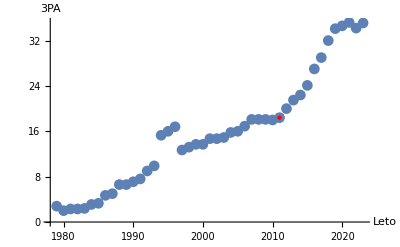

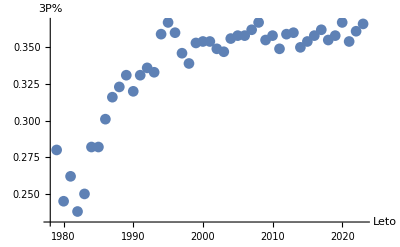

```mathematica
ListPlot[
 TPAData, PlotMarkers->Automatic, AxesLabel->{"Leto","3PA"},
 Epilog->{Red,PointSize@Large,Point[{2011,18.4}]}
 ]
 
ListPlot[
 {TPpData}, PlotMarkers->Automatic, AxesLabel->{"Leto","3P%"}
 ]
```

## Zakaj 2011?

Okoli teh let je uporaba naprednih statistik, postala zelo bolj uporabna, ta pa nam reče da je met za 3 bolj učinkovit.
V ligo pa je okoli tega časa prišel tudi Stephen Curry, kateri je s svojim premikanjem brez žoge in odlično natančnostjo z razdalje zelo pripomogel k popularnosti meta za 3 točke.
Povprečen gledalec košarke pa se je tega dobro zavedal šele leta 2014, ko je Golden State ( ekipa na kateri je Stephen Curry ) zmagala naslov, Curry pa nagrado najboljšega igralca lige.

eFG% = (2P+1.5 * 3P)/FGA

```mathematica
Import["/home/oskar/Downloads/shotChart.png"]
```

-Graphics-

### Izbira metov v 2000-ih

V 2000-ih veliko igralcev ni bilo tako dobrih v zadevanju trojk, tisti ki so zadeli največ točk so to delali večinoma z meti za 2 točki.

```mathematica
Import["/home/oskar/Downloads/KevinGarnettShotChart.png"]
```

-Graphics-

## James Harden ( 2018-19 )

Ta sezona je zanimiva v glavnem zaradi same količine trojk, ki jih je Harden poskušal. Na igro je probal zadeti 13.2 trojk na tekmo in le 11.3 metov za 2 točki. 
	Med drugimi dosežki, je v 31-ih igrah med sezono zadel povprečno kar 41.4 točk.

```mathematica
Import["/home/oskar/Downloads/HardenShotChart.png"]
```

-Graphics-

## Kako naprej?

Do ne dolgo nazaj so ekipe imele dokaj različne pristope k igri. To je še vedno res, vendar ekipe danes vejo, da brez trojk ne bodo zmagale.

{{42.5,Boston Celtics},{39.5,Dallas Mavericks*},{39.3,Sacramento Kings},{38.9,Golden State Warriors},{38.1,Milwaukee Bucks*},{37.8,Memphis Grizzlies},{37.7,Atlanta Hawks},{36.8,Cleveland Cavaliers*},{36.7,Brooklyn Nets},{36.5,Utah Jazz},{36.4,San Antonio Spurs},{36.1,Houston Rockets},{35.8,New York Knicks*},{35.5,Washington Wizards},{35.3,Indiana Pacers*},{34.2,Oklahoma City Thunder*},{34.,Charlotte Hornets},{33.7,Miami Heat*},{33.3,Philadelphia 76ers*},{33.2,Los Angeles Clippers*},{33.2,Portland Trail Blazers},{33.1,Toronto Raptors},{32.7,Minnesota Timberwolves*},{32.6,Phoenix Suns*},{32.6,New Orleans Pelicans*},{32.1,Chicago Bulls},{31.7,Detroit Pistons},{31.4,Los Angeles Lakers*},{31.3,Orlando Magic*},{31.2,Denver Nuggets*}}

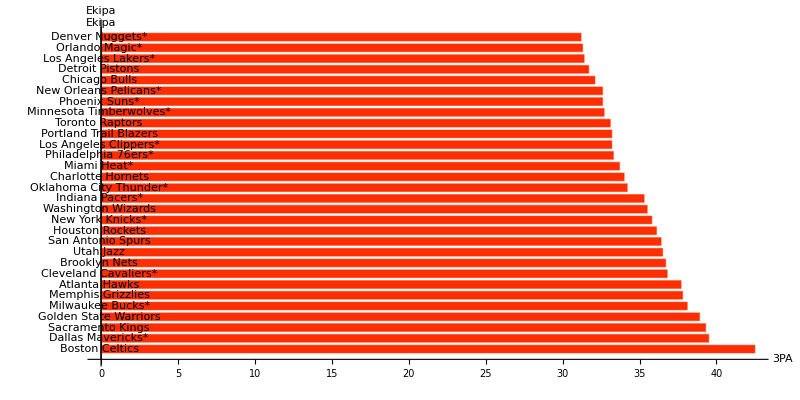

```mathematica
tTPAData = MapThread[List, {tTPA,team}]
BarChart[tTPA,ChartLabels->team, ChartStyle->Hue[.03], AspectRatio->0.5, AxesLabel->{"Ekipa","3PA"},BarOrigin->Left]
```

Letos je naslov lige zmagal Bostom, ki je metal največ poskusov za 3 točke, Dallas, druga ekipa na lestvici, pa je bila njen nasprotnik. V nasportju pa imamo tudi Denver, kateri je na dnu lestvice, vendar je prejšnjo sezono osvojil naslov.

Vprašanje za naprej pa je le ali bo liga nadaljevala v smeri večih metov za tri?

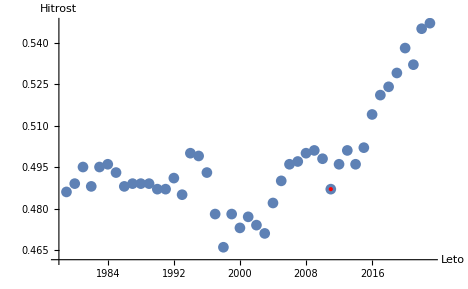

```mathematica
ListPlot[paceData, PlotMarkers->Automatic, AxesLabel->{"Leto","Hitrost"}, Epilog->{Red,PointSize@Large,Point[{2011,0.4870}]}]
```